```mathematica
Remove["Global`*"]
```

```mathematica
kharm =Solve[ν==1/(2Pi)*Sqrt[k/υ],k]
```

{{k→4 π^2 ν^2 υ}}

```mathematica
Vp = (k/2)*x^2
```

(k x^2)/2

```mathematica
Manipulate[Plot[(k x^2)/2,{x,-8,8}],{k,0,8}]
```

```mathematica
Vqm=Vp/. kharm
```

{2 π^2 x^2 ν^2 υ}

```mathematica
(* Dt[f,(x,2}]   find second derivative with respect to x  *)
```

```mathematica
2 π^2 x^2 ν^2 υ*Ψ[x]- h^2/(8*Pi^2*m)*Ψ''[x]==Energy[n] Ψ[x]
```

2 π^2 x^2 ν^2 υ Ψ[x]-(h^2 Ψ''[x])/(8 m π^2)==Energy[n] Ψ[x]

```mathematica
2 π^2 x^2 ν^2 υ Ψ[x]-(h^2 Ψ''[x])/(8 υ π^2)==Energy[n] Ψ[x]
```

2 π^2 x^2 ν^2 υ Ψ[x]-(h^2 Ψ''[x])/(8 π^2 υ)==Energy[n] Ψ[x]

```mathematica
Solution=DSolve[2 π^2 x^2 ν^2 υ*Ψ[x]- h^2/(8*Pi^2*υ)*Ψ''[x]==Energy[n] Ψ[x],Ψ[x],x]
```

{{Ψ[x]→C[2] ParabolicCylinderD[(-h ν-2 Energy[n])/(2 h ν),(2 ⅈ √2 π x √ν √υ)/(√h)]+C[1] ParabolicCylinderD[(-h ν+2 Energy[n])/(2 h ν),(2 √2 π x √ν √υ)/(√h)]}}

```mathematica
PsiSolution=FunctionExpand[Ψ[x]/. Solution]/. C[2]->0
```

{2^(-(-h ν+2 Energy[n])/(4 h ν)) ⅇ^(-(2 π^2 x^2 ν υ)/h) C[1] HermiteH[(-h ν+2 Energy[n])/(2 h ν),(2 π x √ν √υ)/(√h)]}

```mathematica
En[n_]=Solve[(-h ν+2 Energy[n])/(2 h ν)==0+n , Energy[n]]//Flatten
```

{Energy[n]→1/2 h (1+2 n) ν}

```mathematica
Table [En[m],{m,0,4}]
```

{{Energy[0]→(h ν)/2},{Energy[1]→(3 h ν)/2},{Energy[2]→(5 h ν)/2},{Energy[3]→(7 h ν)/2},{Energy[4]→(9 h ν)/2}}

```mathematica
Φ[n_,x_] = Simplify[PsiSolution/. En[n]]// Flatten
```

{2^(-n/2) ⅇ^(-(2 π^2 x^2 ν υ)/h) C[1] HermiteH[n,(2 π x √ν √υ)/(√h)]}

```mathematica
(* Normalize wavefunction *)

Integrate [Φ[1,x]^2, {x,-Infinity, Infinity}]
```

{ConditionalExpression[(ν υ C[1]^2)/(2 h √π ((ν υ)/h)^(3/2)),Re[(ν υ)/h]>0]}

```mathematica
c0[n_,x_]:=Solve[Integrate [Last[Φ[1,x]^2], {x,-Infinity, Infinity},Assumptions->((ν υ)/h)>0]==1,C[1]]
```

```mathematica
Φnx[n_,x_]=Φ[n,x]/. Last[c0[n,x]]
```

{2^(1/2-n/2) ⅇ^(-(2 π^2 x^2 ν υ)/h) π^(1/4) ((ν υ)/h)^(1/4) HermiteH[n,(2 π x √ν √υ)/(√h)]}

```mathematica
Flatten[{{-2^(1/2-n/2) ⅇ^(-(2 π^2 x^2 ν υ)/h) π^(1/4) ((ν υ)/h)^(1/4) HermiteH[n,(2 π x √ν √υ)/(√h)]},{2^(1/2-n/2) ⅇ^(-(2 π^2 x^2 ν υ)/h) π^(1/4) ((ν υ)/h)^(1/4) HermiteH[n,(2 π x √ν √υ)/(√h)]}}]
```

{-2^(1/2-n/2) ⅇ^(-(2 π^2 x^2 ν υ)/h) π^(1/4) ((ν υ)/h)^(1/4) HermiteH[n,(2 π x √ν √υ)/(√h)],2^(1/2-n/2) ⅇ^(-(2 π^2 x^2 ν υ)/h) π^(1/4) ((ν υ)/h)^(1/4) HermiteH[n,(2 π x √ν √υ)/(√h)]}

```mathematica
n=1;
```

```mathematica
Integrate [Φnv[1,x]*Φnv[2,x], {x,-Infinity,Infinity}]
```

∫_(-∞)^∞ Φnv[1,x] Φnv[2,x]ⅆx

```mathematica
(*< x >   is proportional to dipole moment        LET's LOOK at SELECTION RULES  *)
```

```mathematica
n=1
```

1

```mathematica
m=1
```

1

```mathematica
∫_(-∞)^∞ 2^(1/2-n/2) ⅇ^(-(2 π^2 x^2 ν υ)/h) π^(1/4) ((ν υ)/h)^(1/4) HermiteH[n,(2 π x √ν √υ)/(√h)]*x*2^(1/2-m/2) ⅇ^(-(2 π^2 x^2 ν υ)/h) π^(1/4) ((ν υ)/h)^(1/4) HermiteH[m,(2 π x √ν √υ)/(√h)]ⅆx
```

ConditionalExpression[0,Re[(ν υ)/h]≥0]

```mathematica
Integrate [Φnv[1,x]*Φnv[1,x], {x,-Infinity,Infinity}

∫_(-∞)^∞ (2^(1/2-n/2) ⅇ^(-2 π^2 x^2) π^(1/4) HermiteH[n,2 π x])^2 ⅆx
```

∫_(-∞)^∞ Φnv[1,x]^2 ⅆx

∫_(-∞)^∞ 2^(1-n) ⅇ^(-4 π^2 x^2) √π HermiteH[n,2 π x]^2ⅆx

```mathematica
h=1;ν =1; υ=1; n=0;
```

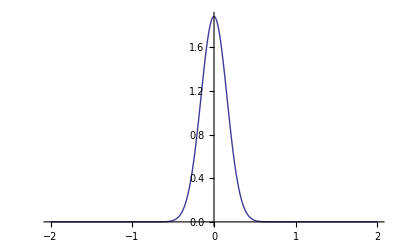

```mathematica
Plot[2^(1/2-n/2) ⅇ^(-2 π^2 x^2) π^(1/4) HermiteH[n,2 π x],{x,-2,2},PlotRange->Full]
```

```mathematica
Manipulate[Plot[2^(1/2-n/2) ⅇ^(-2 π^2 x^2) π^(1/4) HermiteH[n,2 π x],{x,-2,2},PlotRange->Full],{n,0,8,1}]
```

```mathematica
∫_(-∞)^∞ Φ[1,x]^2 ⅆx
```

{C[1]^2/(2 √π)}

```mathematica
∫_(-∞)^∞ Φnx[1,x]^2 ⅆx
```

{1}

```mathematica
N[%]
```

{1.}

```mathematica
Φnx[0,x]
```

{√2 ⅇ^(-2 π^2 x^2) π^(1/4)}

```mathematica
h=(6.626*10^-34*Joule* Second/. Joule->Kilogram*(100 cm)^2/(Second^2) )*(Second/(cm^2*Kilogram))
```

6.626×10^-30

```mathematica
Light =3.0*10^8 Meter/Second
```

(3.×10^8 Meter)/Second

```mathematica
cc=(Light^2/. Meter -> 100 cm)*(Second^2/cm^2)
```

9.×10^20

```mathematica
υ=(12*16)/(12+16)*1.672*10^-27 Kilogram *(1/Kilogram)
```

1.14651×10^-26

```mathematica
waven=2168*cm^-1*(cm)
```

2168

```mathematica
ν=(waven*Light /. Meter -> 100 cm)*(Second/cm)
```

6.504×10^13

```mathematica
fc=k/. kharm;
```

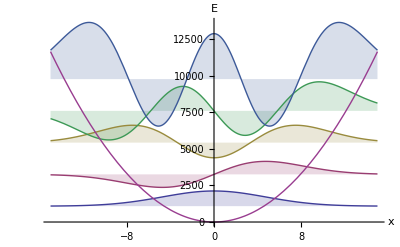

```mathematica
Plot[Evaluate@Append[Table[3.0*10^-2*Φnx[n,x]+ (n+0.5)*waven, {n,0,4}],0.006*cc*fc*x^2/2],{x, -1.5*10^-9,1.5*10^-9}, Filling-> Table[n->(n-0.5)*waven, {n,1,5}], AxesLabel->{x,"E"}]
```

```mathematica
0.006*cc*fc*x^2/2
```

{5.16968×10^21 x^2}

```mathematica
2.7*^19 x^2
```

2.7×10^19 x^2